## Comparing the nuc & cyto intensity measurements of fix cell accumulation 15h experiments

Import the csv file from Measure_cyto_nuc_bkg_AutoThreshold.ijm processed fix cell images, stained with Cy3-FLAG-Fab

```mathematica
myFileName = FileNames["/Users/ccialek/Desktop/temp/20190302_TL_Results.csv" ]
```

{/Users/ccialek/Desktop/temp/20190302_TL_Results.csv}

```mathematica
mycsv = Import [myFileName[[1]]];
```

```mathematica
mycsv[[1]]
```

{,Area,Mean,Min,Max}

```mathematica
mymsrmts = Partition[ Flatten@mycsv[[2;;All]] , 8(*4 bkgd, 2 nuc, 2 cyto*) *5 (*5 measureents, {"","Area","Mean","Min","Max"}*)] ;
```

```mathematica
mymsrmts [[1]]
```

{1,2500,632.456,569,751,2,2500,632.598,554,728,3,2500,606.043,546,702,4,2500,605.158,549,699,5,56393,1015.63,660,2102,6,38189,1050.11,686,2102,7,56393,926.26,602,14823,8,38189,974.202,638,14823}

1.    Channel 1 bkgd1
2.    Channel 1 bkgd2
3.    Channel 2 bkgd1
4.    Channel 2 bkgd2
5.    Channel 1 Cyto
6.    Channel 1 Nuc
7.    Channel 2 Cyto
8.    Channel 2 Nuc

a.    Measurement #
b.    Area of ROI
c.    Mean intensity  
d.    Min intensity
e.    Max intensity

```mathematica
mymsrmts[[All,1;;All;;5]]
```

```mathematica
myAreas = mymsrmts[[All,2;;All;;5]];
myMeans = mymsrmts[[All,3;;All;;5]];
```

```mathematica
ch1bkgs = myMeans[[All,1;;2]];
meanCh1bkgs = Min/@ch1bkgs;
ch2bkgs = myMeans[[All,3;;4]];
meanCh2bkgs = Min/@ch2bkgs;
```

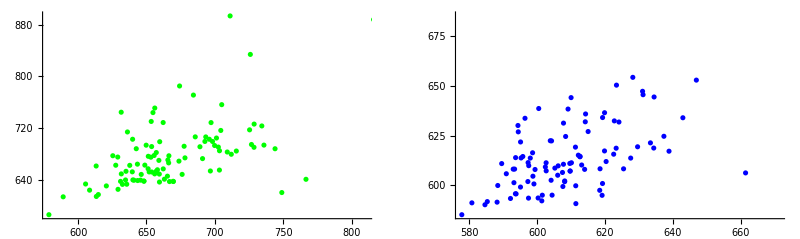

```mathematica
GraphicsRow[{ ListPlot[ch1bkgs, PlotStyle->Green],
ListPlot[ch2bkgs, PlotStyle->Blue]   }]
```